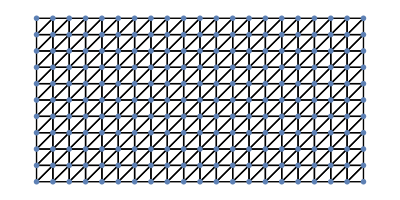
-Graphics-Triangle FEM Geometry Model

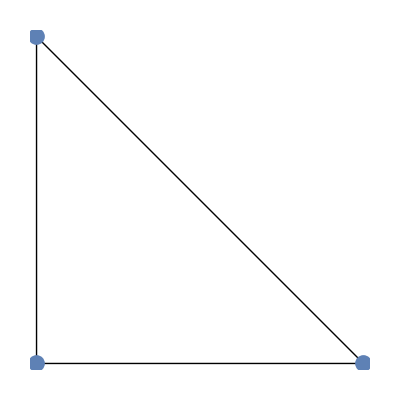
-Graphics-Reference Triangle

```mathematica
Nodes={};
Offst1 = 5.0;
Offst2=5.0;
shwNodes={};
i=1;
xst=0;               
yst=0;
While[xst<100.25,
While[yst<50.25, 
Nodes= Append[Nodes,{i,xst,yst}];
shwNodes=Append[shwNodes,{xst,yst}];
If[yst<50,(*50-5*)
yst = yst+Offst1, 
yst=51.(*51-6*)
];
i++
];
xst=xst+Offst2;
yst=0;
];

PtNodes=ListPlot[shwNodes,AspectRatio->Automatic];
Show[PtNodes];

Elem3={};

i=1;
j=1;
Coln=10; (*50*)
ColLst=Table[i*11,{i,1,20}];(*51*)
While[ i≤400,(*2501*)
Elem3=Append[Elem3,{i,j,j+Coln+1,j+Coln+2}];
Elem3=Append[Elem3,{i+1,j,j+Coln+2,j+1}];
j++;
If[MemberQ[ColLst,j],
j=j+1
];
i=i+2;
];

nodes={};
For[q=1,q≤ Length[Nodes],q++,
AppendTo[nodes,
{
Nodes[[q]][[2]],
Nodes[[q]][[3]]
}
];
];

elements={};

For[p=1,p≤ Length[Elem3],p++,
AppendTo[elements,
{
Elem3[[p]][[2]],
Elem3[[p]][[3]],
Elem3[[p]][[4]]
}
];
];

lines={};
For[w=1,w≤Length[elements],w++,
AppendTo[lines,
Line[{nodes[[elements[[w,1]]]],nodes[[elements[[w,2]]]],nodes[[elements[[w,3]]]],nodes[[elements[[w,1]]]]}]
]
];

RTriangle={{0,0},{1,0},{0,1}};
reflines={};
AppendTo[reflines,
Line[{RTriangle[[1]],RTriangle[[2]],RTriangle[[3]],RTriangle[[1]]}]
];
Print[Show[Graphics[lines],ListPlot[nodes,PlotStyle->PointSize[0.01]]],"Triangle FEM Geometry Model"];
Print[Show[Graphics[reflines],ListPlot[RTriangle,PlotStyle->PointSize[0.03]]],"Reference Triangle"];
```

```mathematica
Vandermonde=ConstantArray[1,{Length[RTriangle],Length[RTriangle]}];
For[g=1,g≤ Length[Vandermonde],g++,

Vandermonde[[g]][[2]]=RTriangle[[g]][[1]];
Vandermonde[[g]][[3]]=RTriangle[[g]][[2]];

];
```

```mathematica
A=Vandermonde;
B=ConstantArray[0,Length[A]];
F={};
K=ConstantArray[0,{Length[nodes],Length[nodes]}];
M=ConstantArray[0,{Length[nodes],Length[nodes]}];

For[i=1,i≤ Length[A],i++,
B[[i]]=1;
AppendTo[F,LinearSolve[A,B].{1,x,y}];
B[[i]]=0;
];

a=γ-α;
b=δ-β;
c=μ-α;
d=ν-β;

T={{a,c},{b,d}};

{inverse1,inverse2}=Ainverse[α_,β_,γ_,δ_,x_,y_]=Inverse[T].{x,y}-Inverse[T].{α,β};

For[k=1,k≤ Length[elements],k++,
For[m=1,m≤ Length[F],m++,
For[n=1,n≤ Length[F],n++,

elementcounter=elements[[k]];
columns=elementcounter[[n]];
rows=elementcounter[[m]];

α=nodes[[elements[[k]]]][[1]][[1]];
β=nodes[[elements[[k]]]][[1]][[2]];
γ=nodes[[elements[[k]]]][[2]][[1]];
δ=nodes[[elements[[k]]]][[2]][[2]];
μ=nodes[[elements[[k]]]][[3]][[1]];
ν=nodes[[elements[[k]]]][[3]][[2]];

Subscript[F, m][x_,y_]=F[[m]];
Subscript[F, n][x_,y_]=F[[n]];

Subscript[P, m][x_,y_]=Simplify[Subscript[F, m][inverse1,inverse2]];
Subscript[P, n][x_,y_]=Simplify[Subscript[F, n][inverse1,inverse2]];

Subscript[G, m]=Grad[Subscript[P, m][x,y],{x,y}];
Subscript[G, n]=Grad[Subscript[P, n][x,y],{x,y}];

Subscript[H, m]=Subscript[P, m][x,y];
Subscript[H, n]=Subscript[P, n][x,y];

If[Mod[k,2] ≠ 0,
K[[rows,columns]]=K[[rows,columns]]+Integrate[Dot[Subscript[G, m],Subscript[G, n]],{x,α,γ},{y,β,((ν-β)/(μ-α))(x-α)+β}];
M[[rows,columns]]=M[[rows,columns]]+NIntegrate[Times[Subscript[H, m],Subscript[H, n]],{x,α,γ},{y,β,((ν-β)/(μ-α))(x-α)+β}];
];

If[Mod[k,2] == 0,
K[[rows,columns]]=K[[rows,columns]]+Integrate[Dot[Subscript[G, m],Subscript[G, n]],{x,α,γ},{y,((δ-β)/(γ-α))(x-α)+β,ν}];
M[[rows,columns]]=M[[rows,columns]]+NIntegrate[Times[Subscript[H, m],Subscript[H, n]],{x,α,γ},{y,((δ-β)/(γ-α))(x-α)+β,ν}];
];
];
];
];
```

```mathematica
dirichlet=ConstantArray[0,Length[nodes]];
dirichlet[[1]]=1;
K[[1]]=dirichlet;
M[[1]]=dirichlet;

evectors=Eigenvectors[{K,M}];
rise=ConstantArray[0,Length[elements]];
plots=ConstantArray[0,Length[nodes]];

For[λ=1,λ≤ Length[nodes],λ++,
For[v=1,v≤ Length[elements],v++,

elementcounter=elements[[v]];

α=nodes[[elements[[v]]]][[1]][[1]];
β=nodes[[elements[[v]]]][[1]][[2]];
γ=nodes[[elements[[v]]]][[2]][[1]];
δ=nodes[[elements[[v]]]][[2]][[2]];
μ=nodes[[elements[[v]]]][[3]][[1]];
ν=nodes[[elements[[v]]]][[3]][[2]];

centerx=(α+γ)/2;
centery=(β+ν)/2;

rise[[v]]={centerx,centery,evectors[[λ]][[ elementcounter[[1]]]]* Subscript[P, 1][x,y]+ evectors[[λ]][[elementcounter[[2]]]]* Subscript[P, 2][x,y]+evectors[[λ]][[ elementcounter[[3]]]]* Subscript[P, 3][x,y]/.{x-> centerx,y-> centery}};

];
plots[[λ]]=ListPlot3D[rise, PlotRange-> All];
];
```

```mathematica
timestart=1;
timefinish=Length[plots];
time=RandomInteger[{timestart,timefinish}];
time1=RandomInteger[{time,timefinish}];
time2=RandomInteger[{time1,timefinish}];

Print[plots[[time]],"3D Plot solution for randomly generated λ = ", time];
Print[plots[[time1]],"3D Plot solution for randomly generated λ = ", time1];
Print[plots[[time2]],"3D Plot solution for randomly generated λ = ", time2];
```

-Graphics3D-3D Plot solution for randomly generated λ = 68

-Graphics3D-3D Plot solution for randomly generated λ = 223

-Graphics3D-3D Plot solution for randomly generated λ = 226